# Autoregressive Process with Non-Normal Innovations

## Laurens Bogaardt | RIVM | SIM | 2019-09-13

In an autoregressive process, at every new time step, a small amount of error is added to the previous value. This is sometimes called an ‘innovation’ or a ‘shock’. The effect of a single shock decays exponentially over time while the overall effect is the sum of all previous shocks, resulting in a meandering time series with temporal autocorrelation. In a first-order autoregressive process, each subsequent value only depends on the previous value, making it a Markov process which describes the step-by-step evolution of a continuous variable. In the limit of small time differences between steps, when many small shocks accumulate, the first-order autoregressive process becomes the Ornstein–Uhlenbeck process. Then, the central limit theorem ensures that the resulting values follow a normal distribution. If shocks themselves are sampled from a normal distribution, this holds for any time difference. However, for larger time steps and non-normal innovations, the resulting distribution may also deviate from normal. This document examines the resulting distribution and time series.

## Initialisation

```mathematica
importPackage=Function[{path},Module[{notebook=NotebookOpen[path,CellContext->"Global`",Visible->False]},NotebookEvaluate[notebook,InsertResults->False,EvaluationElements->"InitializationCell"];NotebookClose[notebook]]];
```

```mathematica
importPackage[ToString[ParentDirectory[NotebookDirectory[]]]<>"/The Sinh-ArcSinh Family of Distributions.nb"]
```

NotebookClose[$Failed]

## Autoregressive Process

```mathematica
processMeanFromInnovations=Function[{equilibrium,errorMean,beta},equilibrium+errorMean/(1-(1-beta)^1)]
processVarianceFromInnovations=Function[{errorVariance,beta},errorVariance/(1-(1-beta)^2)]
processSkewnessFromInnovations=Function[{errorSkewness,beta},errorSkewness(1-(1-beta)^2)^(3/2)/(1-(1-beta)^3)]
processKurtosisFromInnovations=Function[{errorKurtosis,beta},3+(errorKurtosis-3)(1-(1-beta)^2)^(4/2)/(1-(1-beta)^4)]
```

Function[{equilibrium,errorMean,beta},equilibrium+errorMean/(1-(1-beta)^1)]

Function[{errorVariance,beta},errorVariance/(1-(1-beta)^2)]

Function[{errorSkewness,beta},(errorSkewness (1-(1-beta)^2)^(3/2))/(1-(1-beta)^3)]

Function[{errorKurtosis,beta},3+((errorKurtosis-3) (1-(1-beta)^2)^(4/2))/(1-(1-beta)^4)]

```mathematica
innovationsMeanFromProcess=Function[{equilibrium,processMean,beta},(1-(1-beta)^1)(processMean-equilibrium)]
innovationsVarianceFromProcess=Function[{processVariance,beta},(1-(1-beta)^2)processVariance]
innovationsSkewnessFromProcess=Function[{processSkewness,beta},(1-(1-beta)^3)/(1-(1-beta)^2)^(3/2)processSkewness]
innovationsKurtosisFromProcess=Function[{processKurtosis,beta},3+(1-(1-beta)^4)/(1-(1-beta)^2)^(4/2)(processKurtosis-3)]
```

Function[{equilibrium,processMean,beta},(1-(1-beta)^1) (processMean-equilibrium)]

Function[{processVariance,beta},(1-(1-beta)^2) processVariance]

Function[{processSkewness,beta},((1-(1-beta)^3) processSkewness)/((1-(1-beta)^2)^(3/2))]

Function[{processKurtosis,beta},3+((1-(1-beta)^4) (processKurtosis-3))/((1-(1-beta)^2)^(4/2))]

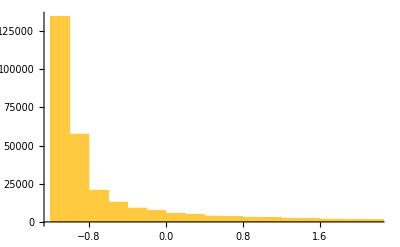
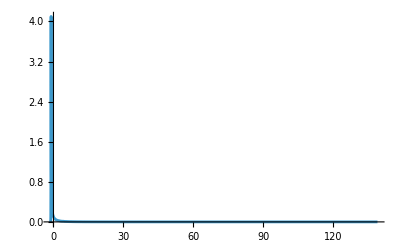
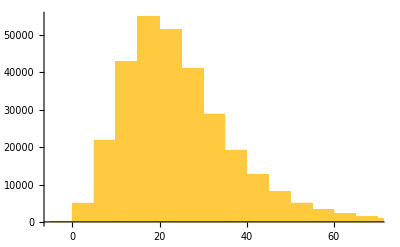
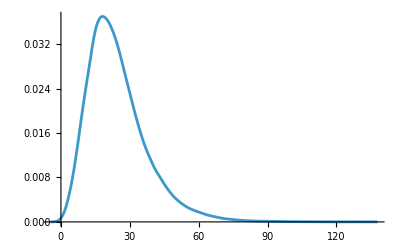
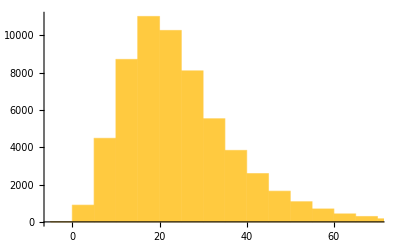
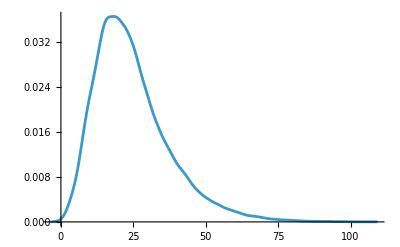
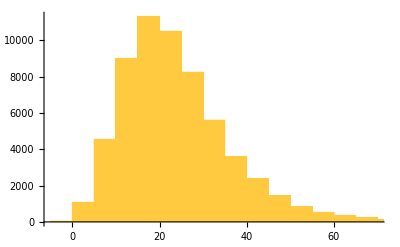
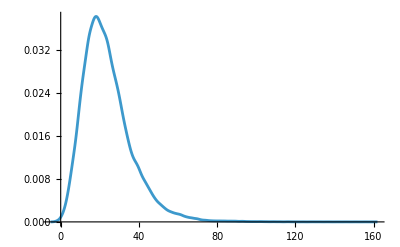
| Mean | Variance | Skewness | Kurtosis
Innovation Moments from Data | 0.00385032 | 10.0638 | 8.0763 | 118.025
Innovation Prediction from Parameters | -0.00433741 | 9.92539 | 8.0862 | 121.232
Innovation Prediction from Process | 0.00386418 | 10.1253 | 7.7687 | 103.999
Process Moments from Data | 24.6288 | 171.325 | 1.27815 | 6.07539
Process Prediction from Parameters | 24.3554 | 167.942 | 1.33038 | 6.60014
Process Prediction from Innovations | 24.6283 | 170.284 | 1.32876 | 6.5025
Distribution Plots | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Distribution over time | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Process Plots | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Process Plots | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
With[{n=300000,equilibrium=24.5,beta=0.03,a=-1.05,b=0.0001,c=2.2,d=0.3},Module[{oldValue=equilibrium,innovations=jonesInverseCumulativeDistribution[RandomReal[{0,1},n],a,b,c,d]},With[{data=Table[With[{newValue=oldValue+beta*(equilibrium-oldValue)+innovation},oldValue=newValue],{innovation,innovations}]},Grid[{{"","Mean","Variance","Skewness","Kurtosis"},{"Innovation Moments from Data",Mean[innovations],Variance[innovations],Skewness[innovations],Kurtosis[innovations]},{"Innovation Prediction from Parameters",jonesRawMoments[1,a,b,c,d],jonesCentralMoments[2,a,b,c,d],jonesStandardisedMoments[3,a,b,c,d],jonesStandardisedMoments[4,a,b,c,d]},{"Innovation Prediction from Process",innovationsMeanFromProcess[equilibrium,Mean[data],beta],innovationsVarianceFromProcess[Variance[data],beta],innovationsSkewnessFromProcess[Skewness[data],beta],innovationsKurtosisFromProcess[Kurtosis[data],beta]},{"Process Moments from Data",Mean[data],Variance[data],Skewness[data],Kurtosis[data]},{"Process Prediction from Parameters",processMeanFromInnovations[equilibrium,jonesRawMoments[1,a,b,c,d],beta],processVarianceFromInnovations[jonesCentralMoments[2,a,b,c,d],beta],processSkewnessFromInnovations[jonesStandardisedMoments[3,a,b,c,d],beta],processKurtosisFromInnovations[jonesStandardisedMoments[4,a,b,c,d],beta]},{"Process Prediction from Innovations",processMeanFromInnovations[equilibrium,Mean[innovations],beta],processVarianceFromInnovations[Variance[innovations],beta],processSkewnessFromInnovations[Skewness[innovations],beta],processKurtosisFromInnovations[Kurtosis[innovations],beta]},{"Distribution Plots",Histogram[innovations],SmoothHistogram[innovations],Histogram[data],SmoothHistogram[data]},{"Distribution over time",Histogram[Take[data,{1/5n,2/5n}]],SmoothHistogram[Take[data,{1/5n,2/5n}]],Histogram[Take[data,{3/5n,4/5n}]],SmoothHistogram[Take[data,{3/5n,4/5n}]]},Join[{"Process Plots"},Table[ListPlot[Take[data,{1000p,1000p+100}]],{p,1,4}]],Join[{"Process Plots"},Table[ListPlot[Take[data,{1000p,1000p+100}]],{p,5,8}]]}]]]]
```

## References

https://en.wikipedia.org/wiki/Autoregressive_model
https://en.wikipedia.org/wiki/Standardized_moment
https://stats.stackexchange.com/questions/103405/prove-expression-for-variance-ar1
https://stats.stackexchange.com/questions/214041/skewness-for-a-sum-of-independent-weighted-bernoulli-random-variables-with-diffe